```mathematica
Get["reran-path-integrals-simulations.m"];
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
haywardScenario1  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,5}]);
```

```mathematica
haywardScenario2  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);
haywardScenario3  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,5}]);
```

```mathematica
haywardScenario4  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,5}]);
```

```mathematica
Clear[pints]
```

```mathematica
start = 0.1;
time = 0.05;
jumpSize = 1;
selectedNe = 500;
fitVar = 1;
```

```mathematica
(* Scenario 1*)
selCoef = 0.005;
genVar = 0.002249954;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

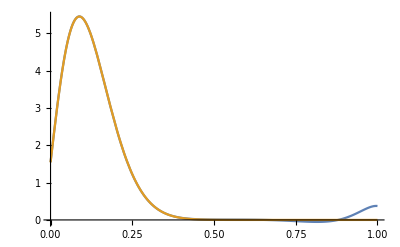

```mathematica
Plot[{Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],8
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.880844}. NIntegrate obtained 0.0325838 and 5.21238×10^-8 for the integral and error estimates.

{{0.0162919}}

```mathematica
Export["SimComparison_Scenario1_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario1_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 1.54718

0.01 xxxx 2.29146

0.02 xxxx 3.00659

0.03 xxxx 3.6597

0.04 xxxx 4.22656

0.05 xxxx 4.69124

0.06 xxxx 5.04534

0.07 xxxx 5.2869

0.08 xxxx 5.41929

0.09 xxxx 5.44997

0.1 xxxx 5.38938

0.11 xxxx 5.24984

0.12 xxxx 5.04469

0.13 xxxx 4.78746

0.14 xxxx 4.49131

0.15 xxxx 4.16853

0.16 xxxx 3.83025

0.17 xxxx 3.4862

0.18 xxxx 3.14462

0.19 xxxx 2.81227

0.2 xxxx 2.49444

0.21 xxxx 2.1951

0.22 xxxx 1.91697

0.23 xxxx 1.66173

0.24 xxxx 1.43014

0.25 xxxx 1.22222

0.26 xxxx 1.03739

0.27 xxxx 0.874627

0.28 xxxx 0.732568

0.29 xxxx 0.609641

0.3 xxxx 0.504149

0.31 xxxx 0.414346

0.32 xxxx 0.338497

0.33 xxxx 0.274927

0.34 xxxx 0.222052

0.35 xxxx 0.178404

0.36 xxxx 0.142645

0.37 xxxx 0.113568

0.38 xxxx 0.0901066

0.39 xxxx 0.0713225

0.4 xxxx 0.0564038

0.41 xxxx 0.0446537

0.42 xxxx 0.0354805

0.43 xxxx 0.0283863

0.44 xxxx 0.0229565

0.45 xxxx 0.018848

0.46 xxxx 0.0157799

0.47 xxxx 0.0135236

0.48 xxxx 0.0118941

0.49 xxxx 0.0107429

0.5 xxxx 0.00995071

0.51 xxxx 0.00942211

0.52 xxxx 0.00908019

0.53 xxxx 0.00886245

0.54 xxxx 0.00871731

0.55 xxxx 0.00860108

0.56 xxxx 0.00847566

0.57 xxxx 0.00830663

0.58 xxxx 0.0080618

0.59 xxxx 0.00771013

0.6 xxxx 0.00722108

0.61 xxxx 0.00656418

0.62 xxxx 0.00570898

0.63 xxxx 0.00462528

0.64 xxxx 0.00328366

0.65 xxxx 0.00165626

0.66 xxxx -0.000282124

0.67 xxxx -0.00255264

0.68 xxxx -0.00517073

0.69 xxxx -0.00814417

0.7 xxxx -0.0114708

0.71 xxxx -0.015136

0.72 xxxx -0.0191101

0.73 xxxx -0.0233451

0.74 xxxx -0.0277717

0.75 xxxx -0.0322963

0.76 xxxx -0.0367974

0.77 xxxx -0.0411228

0.78 xxxx -0.0450867

0.79 xxxx -0.0484676

0.8 xxxx -0.0510065

0.81 xxxx -0.0524068

0.82 xxxx -0.0523352

0.83 xxxx -0.0504245

0.84 xxxx -0.0462791

0.85 xxxx -0.039484

0.86 xxxx -0.0296164

0.87 xxxx -0.016264

0.88 xxxx 0.000952197

0.89 xxxx 0.0223472

0.9 xxxx 0.0481325

0.91 xxxx 0.0783664

0.92 xxxx 0.112891

0.93 xxxx 0.151257

0.94 xxxx 0.192625

0.95 xxxx 0.235652

0.96 xxxx 0.278353

0.97 xxxx 0.317929

0.98 xxxx 0.350567

0.99 xxxx 0.3712

1. xxxx 0.373221

```mathematica
(* Scenario 2*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.01;
genVar = 0.007050979;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

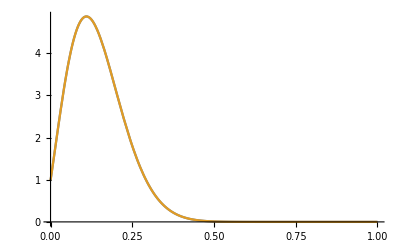

```mathematica
Plot[{Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0683438}. NIntegrate obtained 0.0000217743 and 4.18786×10^-11 for the integral and error estimates.

{{0.0000108872}}

```mathematica
Export["SimComparison_Scenario2_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario2_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 0.987456

0.01 xxxx 1.51896

0.02 xxxx 2.06542

0.03 xxxx 2.60272

0.04 xxxx 3.11001

0.05 xxxx 3.57019

0.06 xxxx 3.97021

0.07 xxxx 4.30098

0.08 xxxx 4.55718

0.09 xxxx 4.73695

0.1 xxxx 4.84134

0.11 xxxx 4.87392

0.12 xxxx 4.84016

0.13 xxxx 4.747

0.14 xxxx 4.60232

0.15 xxxx 4.41449

0.16 xxxx 4.19204

0.17 xxxx 3.94332

0.18 xxxx 3.67625

0.19 xxxx 3.3981

0.2 xxxx 3.11541

0.21 xxxx 2.83385

0.22 xxxx 2.55825

0.23 xxxx 2.29252

0.24 xxxx 2.03975

0.25 xxxx 1.80225

0.26 xxxx 1.58157

0.27 xxxx 1.37867

0.28 xxxx 1.19392

0.29 xxxx 1.02724

0.3 xxxx 0.878196

0.31 xxxx 0.746029

0.32 xxxx 0.629779

0.33 xxxx 0.52833

0.34 xxxx 0.440472

0.35 xxxx 0.364949

0.36 xxxx 0.300504

0.37 xxxx 0.245906

0.38 xxxx 0.199978

0.39 xxxx 0.161613

0.4 xxxx 0.129789

0.41 xxxx 0.103574

0.42 xxxx 0.0821272

0.43 xxxx 0.0647026

0.44 xxxx 0.0506436

0.45 xxxx 0.0393785

0.46 xxxx 0.030415

0.47 xxxx 0.0233329

0.48 xxxx 0.0177767

0.49 xxxx 0.0134489

0.5 xxxx 0.0101023

0.51 xxxx 0.00753332

0.52 xxxx 0.00557601

0.53 xxxx 0.00409599

0.54 xxxx 0.0029855

0.55 xxxx 0.00215882

0.56 xxxx 0.00154835

0.57 xxxx 0.00110123

0.58 xxxx 0.000776508

0.59 xxxx 0.000542702

0.6 xxxx 0.000375844

0.61 xxxx 0.000257847

0.62 xxxx 0.000175181

0.63 xxxx 0.000117826

0.64 xxxx 0.0000784264

0.65 xxxx 0.00005164

0.66 xxxx 0.000033622

0.67 xxxx 0.0000216353

0.68 xxxx 0.0000137517

0.69 xxxx 8.62785×10^-6

0.7 xxxx 5.33817×10^-6

0.71 xxxx 3.25266×10^-6

0.72 xxxx 1.94764×10^-6

0.73 xxxx 1.14193×10^-6

0.74 xxxx 6.51422×10^-7

0.75 xxxx 3.5734×10^-7

0.76 xxxx 1.84264×10^-7

0.77 xxxx 8.51324×10^-8

0.78 xxxx 3.11362×10^-8

0.79 xxxx 4.99227×10^-9

0.8 xxxx -3.47674×10^-9

0.81 xxxx -2.21702×10^-10

0.82 xxxx 1.11738×10^-8

0.83 xxxx 2.82996×10^-8

0.84 xxxx 4.91659×10^-8

0.85 xxxx 7.17432×10^-8

0.86 xxxx 9.37199×10^-8

0.87 xxxx 1.1243×10^-7

0.88 xxxx 1.24937×10^-7

0.89 xxxx 1.28276×10^-7

0.9 xxxx 1.19794×10^-7

0.91 xxxx 9.75859×10^-8

0.92 xxxx 6.08462×10^-8

0.93 xxxx 9.8918×10^-9

0.94 xxxx -5.4491×10^-8

0.95 xxxx -1.33242×10^-7

0.96 xxxx -2.33655×10^-7

0.97 xxxx -3.78182×10^-7

0.98 xxxx -6.19564×10^-7

0.99 xxxx -1.06556×10^-6

1. xxxx -1.91744×10^-6

```mathematica
(* Scenario 3*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.005;
genVar = 0.019860999;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

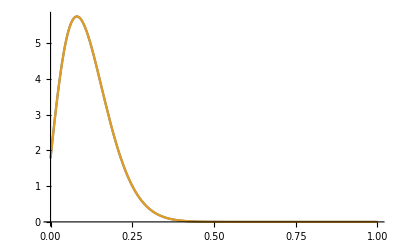

```mathematica
Plot[{Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{9.98602×10^-6}}

```mathematica
Export["SimComparison_Scenario3_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario3_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 1.78163

0.01 xxxx 2.63173

0.02 xxxx 3.428

0.03 xxxx 4.13295

0.04 xxxx 4.7213

0.05 xxxx 5.17876

0.06 xxxx 5.50051

0.07 xxxx 5.68945

0.08 xxxx 5.75431

0.09 xxxx 5.70804

0.1 xxxx 5.56616

0.11 xxxx 5.34551

0.12 xxxx 5.06313

0.13 xxxx 4.73544

0.14 xxxx 4.37759

0.15 xxxx 4.00313

0.16 xxxx 3.62368

0.17 xxxx 3.24893

0.18 xxxx 2.8866

0.19 xxxx 2.54258

0.2 xxxx 2.22107

0.21 xxxx 1.92483

0.22 xxxx 1.65531

0.23 xxxx 1.41297

0.24 xxxx 1.1974

0.25 xxxx 1.00758

0.26 xxxx 0.842011

0.27 xxxx 0.698899

0.28 xxxx 0.576258

0.29 xxxx 0.472029

0.3 xxxx 0.384152

0.31 xxxx 0.310634

0.32 xxxx 0.24959

0.33 xxxx 0.199277

0.34 xxxx 0.158105

0.35 xxxx 0.124654

0.36 xxxx 0.0976637

0.37 xxxx 0.0760376

0.38 xxxx 0.0588281

0.39 xxxx 0.0452263

0.4 xxxx 0.0345487

0.41 xxxx 0.0262234

0.42 xxxx 0.019776

0.43 xxxx 0.0148168

0.44 xxxx 0.0110282

0.45 xxxx 0.00815372

0.46 xxxx 0.00598783

0.47 xxxx 0.00436718

0.48 xxxx 0.00316304

0.49 xxxx 0.00227472

0.5 xxxx 0.00162411

0.51 xxxx 0.00115108

0.52 xxxx 0.000809714

0.53 xxxx 0.00056523

0.54 xxxx 0.000391479

0.55 xxxx 0.000268968

0.56 xxxx 0.000183278

0.57 xxxx 0.000123836

0.58 xxxx 0.0000829481

0.59 xxxx 0.0000550655

0.6 xxxx 0.0000362201

0.61 xxxx 0.0000235989

0.62 xxxx 0.0000152254

0.63 xxxx 9.72385×10^-6

0.64 xxxx 6.14527×10^-6

0.65 xxxx 3.84159×10^-6

0.66 xxxx 2.37446×10^-6

0.67 xxxx 1.45046×10^-6

0.68 xxxx 8.75236×10^-7

0.69 xxxx 5.21424×10^-7

0.7 xxxx 3.06516×10^-7

0.71 xxxx 1.77681×10^-7

0.72 xxxx 1.01498×10^-7

0.73 xxxx 5.70932×10^-8

0.74 xxxx 3.15982×10^-8

0.75 xxxx 1.7191×10^-8

0.76 xxxx 9.18493×10^-9

0.77 xxxx 4.81401×10^-9

0.78 xxxx 2.4721×10^-9

0.79 xxxx 1.24209×10^-9

0.8 xxxx 6.09648×10^-10

0.81 xxxx 2.91746×10^-10

0.82 xxxx 1.35801×10^-10

0.83 xxxx 6.12764×10^-11

0.84 xxxx 2.66838×10^-11

0.85 xxxx 1.11339×10^-11

0.86 xxxx 4.42913×10^-12

0.87 xxxx 1.70775×10^-12

0.88 xxxx 6.61226×10^-13

0.89 xxxx 3.45196×10^-13

0.9 xxxx 2.10419×10^-13

0.91 xxxx 1.01727×10^-13

0.92 xxxx 2.22061×10^-14

0.93 xxxx -2.24705×10^-13

0.94 xxxx -3.25691×10^-13

0.95 xxxx -3.5682×10^-13

0.96 xxxx -2.54284×10^-13

0.97 xxxx -1.87579×10^-13

0.98 xxxx 2.7298×10^-14

0.99 xxxx 8.00541×10^-13

1. xxxx 2.69032×10^-12

```mathematica
(* Scenario 4*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.01;
genVar = 0.056859878;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

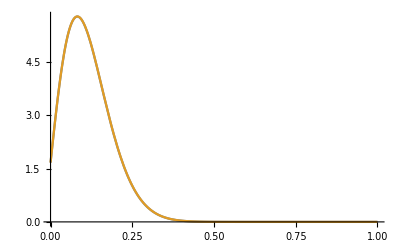

```mathematica
Plot[{Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{0.000483077}}

```mathematica
Export["SimComparison_Scenario4_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario4_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 1.66656

0.01 xxxx 2.51593

0.02 xxxx 3.32194

0.03 xxxx 4.04378

0.04 xxxx 4.65308

0.05 xxxx 5.13297

0.06 xxxx 5.47661

0.07 xxxx 5.68542

0.08 xxxx 5.76724

0.09 xxxx 5.73452

0.1 xxxx 5.60267

0.11 xxxx 5.3887

0.12 xxxx 5.10998

0.13 xxxx 4.78338

0.14 xxxx 4.42457

0.15 xxxx 4.04758

0.16 xxxx 3.66451

0.17 xxxx 3.28545

0.18 xxxx 2.91848

0.19 xxxx 2.56977

0.2 xxxx 2.24375

0.21 xxxx 1.9433

0.22 xxxx 1.67

0.23 xxxx 1.42433

0.24 xxxx 1.20592

0.25 xxxx 1.01373

0.26 xxxx 0.846232

0.27 xxxx 0.701589

0.28 xxxx 0.577768

0.29 xxxx 0.472657

0.3 xxxx 0.384147

0.31 xxxx 0.310197

0.32 xxxx 0.24888

0.33 xxxx 0.198415

0.34 xxxx 0.157182

0.35 xxxx 0.123733

0.36 xxxx 0.096788

0.37 xxxx 0.0752341

0.38 xxxx 0.0581108

0.39 xxxx 0.0446005

0.4 xxxx 0.0340134

0.41 xxxx 0.0257732

0.42 xxxx 0.0194032

0.43 xxxx 0.0145125

0.44 xxxx 0.010783

0.45 xxxx 0.00795862

0.46 xxxx 0.00583439

0.47 xxxx 0.00424789

0.48 xxxx 0.0030713

0.49 xxxx 0.00220493

0.5 xxxx 0.00157157

0.51 xxxx 0.00111194

0.52 xxxx 0.000780854

0.53 xxxx 0.000544168

0.54 xxxx 0.000376265

0.55 xxxx 0.000258091

0.56 xxxx 0.000175582

0.57 xxxx 0.000118448

0.58 xxxx 0.0000792151

0.59 xxxx 0.0000525071

0.6 xxxx 0.0000344859

0.61 xxxx 0.0000224364

0.62 xxxx 0.0000144551

0.63 xxxx 9.21931×10^-6

0.64 xxxx 5.8188×10^-6

0.65 xxxx 3.63294×10^-6

0.66 xxxx 2.24282×10^-6

0.67 xxxx 1.36851×10^-6

0.68 xxxx 8.24911×10^-7

0.69 xxxx 4.9096×10^-7

0.7 xxxx 2.88349×10^-7

0.71 xxxx 1.67015×10^-7

0.72 xxxx 9.53371×10^-8

0.73 xxxx 5.35945×10^-8

0.74 xxxx 2.96468×10^-8

0.75 xxxx 1.61229×10^-8

0.76 xxxx 8.61158×10^-9

0.77 xxxx 4.51235×10^-9

0.78 xxxx 2.31649×10^-9

0.79 xxxx 1.1633×10^-9

0.8 xxxx 5.70256×10^-10

0.81 xxxx 2.72122×10^-10

0.82 xxxx 1.2583×10^-10

0.83 xxxx 5.5984×10^-11

0.84 xxxx 2.36862×10^-11

0.85 xxxx 9.26005×10^-12

0.86 xxxx 3.21539×10^-12

0.87 xxxx 1.00109×10^-12

0.88 xxxx 3.13142×10^-13

0.89 xxxx 3.79035×10^-13

0.9 xxxx 6.16512×10^-13

0.91 xxxx 5.4489×10^-13

0.92 xxxx 2.05213×10^-13

0.93 xxxx -7.67797×10^-13

0.94 xxxx -2.32109×10^-12

0.95 xxxx -4.28785×10^-12

0.96 xxxx -5.30986×10^-12

0.97 xxxx -3.08667×10^-12

0.98 xxxx 4.91699×10^-12

0.99 xxxx 1.29535×10^-11

1. xxxx -2.47996×10^-11